```mathematica
<< MaTeX`
```

## Константы

```mathematica
kB= 1.38 10^-23;
ℏ = 1.054571817 10^-34;
Na = 6.02 10^23;
R = Na kB;
m = 0.007 / Na;
```

```mathematica
ClearAll[GetP];
GetP[T_] := 133.32 10^(10.3454 -8345.57/T-8.84 10^-5 T - 0.68106 Log10[T]);
```

## Данные

```mathematica
path = "D:\\Kami\\git_folder\\notes_5sem\\rqc\\data_processing_3\\data.xlsx";
obj = Import[path,{"Dataset",1},"HeaderLines"->1];
```

```mathematica
ts = Normal@obj[All, "t"];
hs = Normal@obj[All, "h"];
ds = Normal@obj[All, "d"];
Ks = Normal@obj[All, "K"];
```

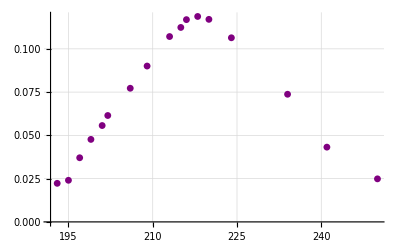

```mathematica
ListPlot[Transpose[{ts, hs/1000}], Joined->False, PlotMarkers->{Automatic,7}, PlotStyle->Purple, GridLines->Automatic, AxesLabel->{MaTeX["t"], MaTeX["h"]}]
```

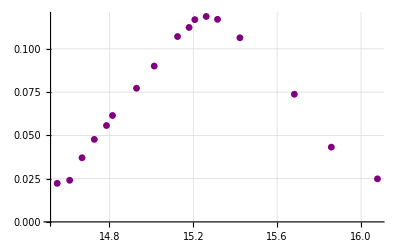

```mathematica
Ts=  ts+273+50;
ns = Map[GetP[ #]/(kB #)&, Ts];
ListPlot[Transpose[{Log10@ns, hs/1000}], Joined->False, PlotMarkers->{Automatic,7}, PlotStyle->Purple, GridLines->Automatic, AxesLabel->{MaTeX["\\log_{10} n"], MaTeX["h"]}]
```

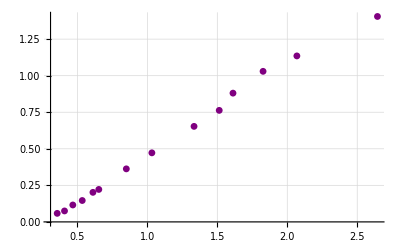

```mathematica
dots = Transpose[{ns / 10^15, -Log[(1-ds/1000)]}]⟦4;;⟧;
fit = NonlinearModelFit[dots, α x, {α}, x];
ListPlot[dots, Joined->False, PlotMarkers->{Automatic,7}, PlotStyle->Purple, GridLines->Automatic, AxesLabel->{MaTeX["n \\times 10^{-15}"], MaTeX["-\\log \\beta"]}, PlotRange->{Full, Full}]
```

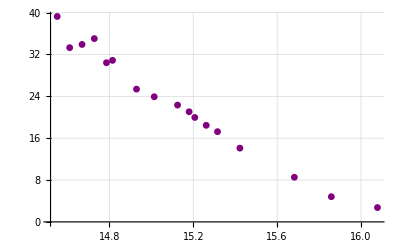

```mathematica
ListPlot[Transpose[{Log10@ns, Ks}], Joined->False, PlotMarkers->{Automatic,7}, PlotStyle->Purple, GridLines->Automatic, AxesLabel->{MaTeX["\\log_{10} n"], MaTeX["K"]}]
```

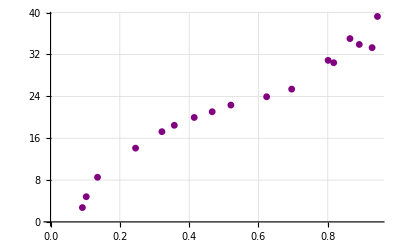

```mathematica
ListPlot[Transpose[{1-ds/1000, Ks}], Joined->False, PlotMarkers->{Automatic,7}, PlotStyle->Purple, GridLines->Automatic, AxesLabel->{MaTeX["\\beta"], MaTeX["K"]}]
```

## Теория

```mathematica
ν0 = (3. 10^8)/(670 10^-9)/10^6; (* МГц *)
c = 3 10^8; (* м/c *)
Γ = 6 10^6 /10^6(* МГц *);
vQ = 1200; (* м/c *)
```

```mathematica
ClearAll[f1];
f1[s_, ν_] := f1[s, ν] = NIntegrate[
(1-s/(1 +s+ 4 (ν - ν0(1+ v/c))^2/Γ^2))
1/(1  + 4 (ν - ν0(1- v/c))^2/Γ^2)Exp[- v^2/vQ^2], {v, -4 vQ, + 4 vQ}, MaxRecursion->12];
```

```mathematica
f1[0, ν0]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

6.30268

```mathematica
f1[10, ν0]
```

1.89205

```mathematica
ClearAll[FF];
FF[T_] := 0.2 2.1 10^-13 √(m/(2 π kB))1/(√T)GetP[T]/(kB T);
Getn[T_] := GetP[T]/(kB T);
```

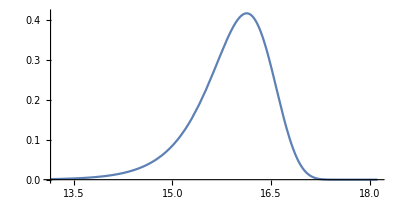

```mathematica
ParametricPlot[{Log10@Getn[T], Exp[-FF[T]f1[10, ν0]]- Exp[-FF[T]f1[0, ν0]]}, {T, 473, 673}, AspectRatio->1/2, AxesLabel->{MaTeX@"\\log_{10} n", MaTeX@"h"}]
```

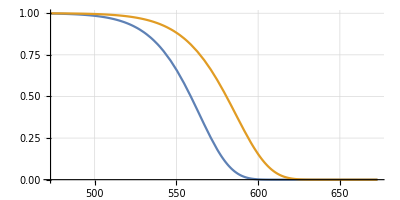

```mathematica
ParametricPlot[{
{T, Exp[-FF[T]f1[0, ν0]]},
{T, Exp[-FF[T]f1[10, ν0]]}}, {T, 473, 673}, AspectRatio->1/2, AxesLabel->{MaTeX@"T, \\ \\text{K}", MaTeX@"I_\\text{out}/I_\\text{in}"}, GridLines->Automatic]
```

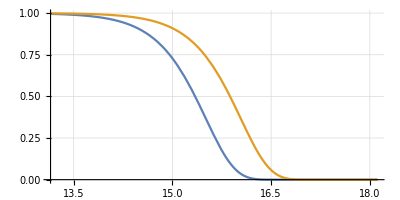

```mathematica
ParametricPlot[{
{Log10@Getn[T], Exp[-FF[T]f1[0, ν0]]},
{Log10@Getn[T], Exp[-FF[T]f1[10, ν0]]}}, {T, 473, 673}, AspectRatio->1/2, AxesLabel->{MaTeX@"\\log_{10} n", MaTeX@"I_\\text{out}/I_\\text{in}"}, GridLines->Automatic]
```

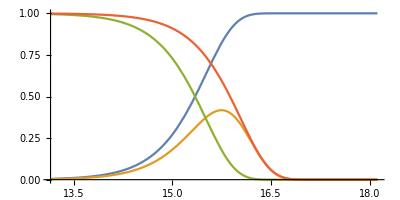

```mathematica
ParametricPlot[{
{Log10@Getn[T], 1-Exp[-FF[T]f1[0, ν0]]},
{Log10@Getn[T], Exp[-FF[T]f1[10, ν0]]- Exp[-FF[T]f1[0, ν0]]},
{Log10@Getn[T], Exp[-FF[T]f1[0, ν0]]},
(*{Log10@Getn[T],(Exp[-FF[T]f1[10, ν0]]- Exp[-FF[T]f1[0, ν0]])/(1-Exp[-FF[T]f1[0, ν0]])},*)
{Log10@Getn[T], Exp[-FF[T]f1[10, ν0]]}}, {T, 473, 673}, AspectRatio->1/2, AxesLabel->{MaTeX@"\\log_{10} n"}]
```

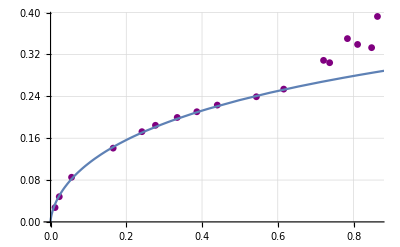

```mathematica
Show[{
ListPlot[Transpose[{1-ds/1000-0.08, Ks/100}], Joined->False, PlotMarkers->{Automatic,7}, PlotStyle->Purple, GridLines->Automatic, AxesLabel->{MaTeX["\\beta"], MaTeX["K"]}],
ParametricPlot[{Exp[-FF[T]f1[0, ν0]],(Exp[-FF[T]f1[1.05, ν0]]- Exp[-FF[T]f1[0, ν0]])/(1-Exp[-FF[T]f1[0, ν0]])}, {T, 473, 673}, AspectRatio->1/2, AxesLabel->{MaTeX@"\\beta", MaTeX@K}, GridLines->Automatic]
}]
```

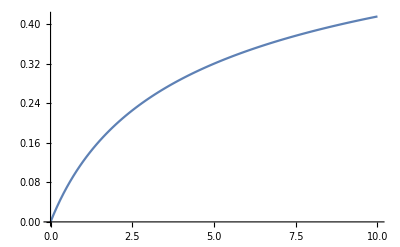

```mathematica
DiscretePlot[Exp[-FF[573]f1[sp, ν0]]- Exp[-FF[573]f1[0, ν0]], {sp, 0, 10, 0.1}, Joined->True, Filling->False]
```